To-do:

1. Sanity Check the RetAmps for L=5,L=4 . (first calc the Lanczos Coeffs).

2. Change the Moments method to be Do loop to avoid Div by zero errors.

3. Check Lanczos Coeff truncation point accuracy for L=4, L=5. (less important)

4. Calc Ret Amps for larger L. (Determine the L=6 HPC bottleneck)
4.1. Try running again on HPC, with Memory usage checks. $MemoryInUse[], and htop, etc.
Expand, Chop, Rationalize coeffs, Simplify, Unrationalize coeffs
Expand, Chop, Group by Exponentials, Parallel simplify
4.2 Try DeveloperToPackedArray
4.3 When done, sanity check at 1. again

5. Lanczos method with FRO/PRO to compare Lanczos coeffs to Moments Method.

# Testing ReturnAmps by checking probability amplitude coverage

```mathematica
L=6;J=1;
tMax=100;
tPts=300;
Prec=40;
tVals = N[Table[tMax*(i)/(tPts), {i, 1, tPts}], Prec];
```

## Importing Return Amplitudes

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\daisy\OneDrive - University of Cape Town\0. Masters Project\Return Amplitudes

### L=4, L=5, L=6

```mathematica
RetAmpsL4=ToExpression[Import["ReturnAmpNumL4TFIM.txt"]];
```

```mathematica
RetAmpsL5=ToExpression[Import["ReturnAmpNumL5TFIM.txt"]];
```

```mathematica
RetAmpChopL5=ToExpression[Import["ReturnAmpChopL5TFIM.txt"]];
```

```mathematica
RetAmpChopL6=ToExpression[Import["ReturnAmpChopL6TFIM.txt"]];
```

```mathematica
RetAmpL6sx=ToExpression[Import["ReturnAmpNumL6TFIMsx.txt"]];
```

```mathematica
RetAmpJacoL6sx=ToExpression[Import["ReturnAmpJacoL6TFIMsx.txt"]];
```

```mathematica
RetAmpChopL6sx=ToExpression[Import["ReturnAmpChopL6TFIMsx.txt"]];
```

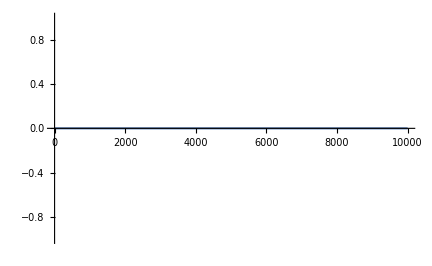

```mathematica
Plot[RetAmpChopL6sx-RetAmpJacoL6sx,{t,0,10000}]
```

```mathematica
{RetAmpJacoL6cd1, RetAmpJacoL6cd2, RetAmpJacoL6cd3, RetAmpJacoL6cd4}=ToExpression[Import["ReturnAmpJacoL6TFIMcd1234.txt"]];
```

### L=7

```mathematica
RetAmpChopL7sx=ToExpression[Import["ReturnAmpChopL7TFIMsx.txt"]];
```

```mathematica
RetAmpChopL7sz=ToExpression[Import["ReturnAmpChopL7TFIMsz.txt"]];
```

```mathematica
{RetAmpJacoL7sp1, RetAmpJacoL7sp2, RetAmpJacoL7sp3, RetAmpJacoL7sp4}=ToExpression[Import["ReturnAmpJacoL7TFIMsp1234.txt"]];
```

```mathematica
{RetAmpJacoL7cd1, RetAmpJacoL7cd2, RetAmpJacoL7cd3, RetAmpJacoL7cd4}=ToExpression[Import["ReturnAmpJacoL7TFIMcd1234.txt"]];
```

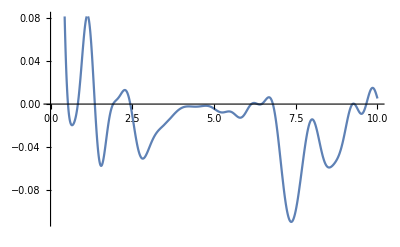

```mathematica
Plot[RetAmpJacoL7cd4,{t,0,10}]
```

### L=8

```mathematica
{RetAmpJacoL8cd1, RetAmpJacoL8cd2, RetAmpJacoL8cd3, RetAmpJacoL8cd4}=ToExpression[Import["ReturnAmpJacoL8TFIMcd1234.txt"]];
```

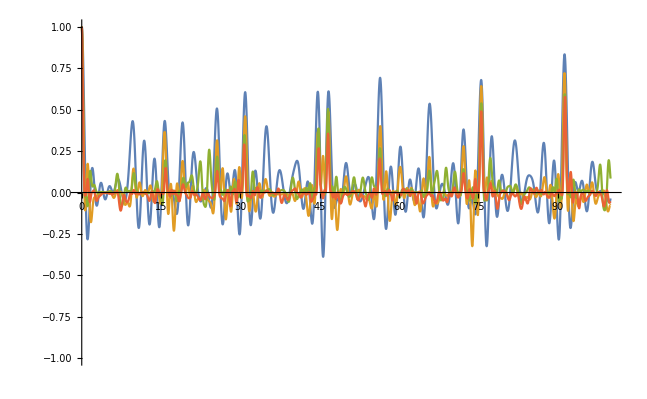

```mathematica
Plot[{RetAmpJacoL8cd1, RetAmpJacoL8cd2, RetAmpJacoL8cd3, RetAmpJacoL8cd4},{t,0,100}, PlotRange->{-1,1}]
```

```mathematica
{RetAmpJacoL8sp1, RetAmpJacoL8sp2, RetAmpJacoL8sp3, RetAmpJacoL8sp4}=ToExpression[Import["ReturnAmpJacoL8TFIMsp1234.txt"]];
```

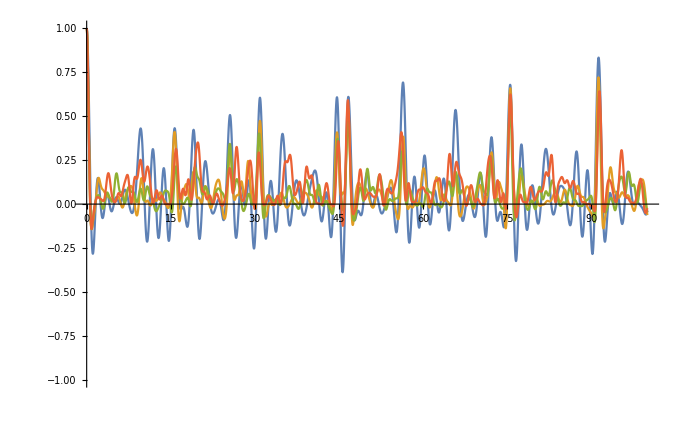

```mathematica
Plot[{RetAmpJacoL8sp1, RetAmpJacoL8sp2, RetAmpJacoL8sp3, RetAmpJacoL8sp4},{t,0,100},PlotRange->{-1,1}]
```

## Functions to take tensor products of local operators

```mathematica
(*Given a binary number occupation rep of spins, it gives the corresponding matrix by taking a tensor product along the chain*)
ChainOccRepTensorProduct[OccRep_, Spin_] := Module[{a}, 
a=IdentityMatrix[1];
Do[ If[OccRep[[i]]==0, a = KroneckerProduct[a,IdentityMatrix[Dimensions[Spin]]]];
If[OccRep[[i]]==1, a = KroneckerProduct[a, Spin]];
,{i, 1, Length[OccRep]}];
a]
```

```mathematica
(*Takes Tensor product along the chain, with operator at position Position, and identities everywhere else*)
ChainTensorProduct[Length_,Operator_,Position_]:=Module[{list,chain},
list=ConstantArray[IdentityMatrix[2],Length];list[[Position]]=Operator;
chain=Apply[KroneckerProduct,list]]
```

```mathematica
(*Takes Tensor product along the chain, with operators at position Position and Position +1, and identities everywhere else*)
ChainNeighbourTensorProduct[Length_,Operator1_,Operator2_,Position_,PBC_:False]:=Module[{list,chain}, 
list=ConstantArray[IdentityMatrix[2],Length];
If[Position==Length, list[[Position]]=Operator1;list[[1]]=Operator2,list[[Position]]=Operator1;list[[Position+1]]=Operator2];
chain=Apply[KroneckerProduct,list]]
```

```mathematica
JordanWignerTensorProduct[Length_,StringOperator_,Operator_,Position_]:=Module[{list,chain},
list=Join[ConstantArray[StringOperator,Position-1],{Operator},ConstantArray[IdentityMatrix[2],Length-Position]];
chain=Apply[KroneckerProduct,list]]
```

## Functions to make Matrices for Ising Chain Hamiltonian and Operators

```mathematica
HIsingIntMode[n_]:=-J*ChainNeighbourTensorProduct[L,PauliMatrix[3],PauliMatrix[3],n];
HIsingBMode[n_]:=-J*ChainTensorProduct[L,PauliMatrix[1],n];
```

```mathematica
HIsing = Sum[HIsingIntMode[n],{n,1,L-1}]+Sum[HIsingBMode[n],{n,1,L}];
MatrixForm[HIsing];
HIsingNormed = HIsing/Sqrt[DocInnerProd[HIsing,HIsing]];
```

### Operators

```mathematica
σPlus0={{0,1},{0,0}};
σMinus0={{0,0},{1,0}};
```

```mathematica
σzMode[n_] := ChainTensorProduct[L, PauliMatrix[3], n];
σyMode[n_] := ChainTensorProduct[L, PauliMatrix[2], n];
σxMode[n_] := ChainTensorProduct[L, PauliMatrix[1], n];
σPlusMode[n_] := ChainTensorProduct[L, σPlus0, n];
σMinusMode[n_] := ChainTensorProduct[L, σMinus0, n];
```

```mathematica
σz = Sum[σzMode[n],{n,1,L}];
σy = Sum[σyMode[n],{n,1,L}];
σx = Sum[σxMode[n],{n,1,L}];
σPlus = Sum[σPlusMode[n],{n,1,L}]; 
σMinus = Sum[σMinusMode[n],{n,1,L}];
```

### Non-local Operators

c_i= Π_(j<i)(σ^z)_j(σ^-)_i
(c^+)_i= Π_(j<i)(σ^z)_j(σ^+)_i

```mathematica
ccMode[n_]:=JordanWignerTensorProduct[L,PauliMatrix[3],σMinus0,n];
cdMode[n_]:=JordanWignerTensorProduct[L,PauliMatrix[3],σPlus0,n];
```

```mathematica
ccc=Sum[ccMode[n],{n,1,L}];
cdc = Sum[cdMode[n], {n, 1, L}];
MatrixForm[ccc]
MatrixForm[cdc]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | -1 | 0)

(0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Functions for Lanczos Coeffs, and Probability Amplitudes

```mathematica
DocInnerProd[A_,B_]:=Conjugate[Flatten[A]].Flatten[B]
```

```mathematica
comm[A_,B_]:=A.B-B.A
```

```mathematica
(*Generate set with repeated actions of Liouvillian on state Op*)
InitialBasis[H_,Op_,n_,prec_]:=
Module[{B},B=N[NestList[comm[H,#]&,Op,n],prec]]
```

```mathematica
(*Generate Othogonal Basis*)
OrthoBasis[H_,Op_,n_,prec_]:=
Module[{B},B=Orthogonalize[InitialBasis[H,Op,n-1,prec],DocInnerProd, Method->"GramSchmidt",Tolerance->10^(-10)]]
```

```mathematica
(*Extract b_ns from the off-diagonals of the Louivillian in the Krylov Basis*)
LanczosOrthog[H_,Op_,nmax_,prec_]:=
Module[{B,a,b},
B=OrthoBasis[H,Op,nmax,prec];
a=Table[DocInnerProd[B[[n]],comm[H,B[[n]]]],{n,1,nmax-1}];
b=Table[DocInnerProd[B[[n-1]],comm[H,B[[n]]]],{n,2,nmax-1}];
{a,b}]
```

```mathematica
Needs["Combinatorica`"]
MomentsMethod2[ReturnAmplitude_, N_]:=Module[{NNNn,nnn,μTab,MijR,bProd,bTab,aTab},
nnn=N*2;
NNNn[t_] := Series[ReturnAmplitude, {t, 0, nnn} ];
μTab = Table[Factorial[j]SeriesCoefficient[ NNNn[t], j], {j, 0, nnn}];

MijR =  Sum[Table[KroneckerDelta[i+j+1-mm]*μTab[[mm]], {i, 0, (nnn)/2}, {j, 0, (nnn)/2}], {mm, 1, Length[μTab]}]   ; 
bProd = Table[Det[MijR[[1;;k, 1;;k]]      ]/Det[MijR[[1;;(k-1), 1;;(k-1)]]      ], {k, 2, nnn/2+1}];  

Print[Table[Precision[bProd[[i]]],{i,1,Length[bProd]}]];

bTab = Table[If[j==1, Sqrt[- bProd[[j]]   ],  Sqrt[- bProd[[j]]/bProd[[j-1]]    ]   ], {j, 1, Length[bProd]}];    
aTab=Table[Simplify[-I(    Simplify[   Cofactor[MijR[[1;;k, 1;;k]], {k-1,k}]/Det[MijR[[1;;k-1, 1;;k-1]]]   ] -    If[k > 2,   Cofactor[MijR[[1;;k-1, 1;;k-1]], {k-2,k-1}]/Det[MijR[[1;;k-2, 1;;k-2]]]    , 0])   ]  , {k, 2, Length[bTab]}   ]; 
{Re[aTab], Re[bTab]} 
]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
TruncateListRightZeros[list_]:=Module[{pos,backwardslist,len},
backwardslist=Reverse[list];pos=LengthWhile[backwardslist,#==0&];len=Length[list];
If[pos==len,list,Take[list,len-pos]]]
```

```mathematica
AmplitudeCoefficient[as_,Bs_,ReturnAmp_,tVals_,Prec_]:=Module[{bs,ϕPts,NNND,NNNDTab,Genf,FtoNSwap,ϕt,cc,PTab},
bs=Bs[[1;;-1-LengthWhile[Reverse@Bs,#==0&]]];
 ϕPts = Length[bs];
(*"Here the derivatives are computed at the time-points.  "*)
	 NNND[0] = ReturnAmp;
	Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];
	NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts}];
	Genf=F[t];
	(*"The substitution to the function F(t)"*)
	FtoNSwap = Table[D[F[t], {t,k}] -> NNNDTab[[k+1]], {k, 0, ϕPts}];
	 ϕt = Table[D[ Genf  , {t, k}], {k, 0, ϕPts}]/.FtoNSwap;
(*"Here we compute the coefficeints cc "*)
	Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]], Prec]  , {n, 0, ϕPts-1}, {m, 0, n+1}]; 
PTab = Table[  Sum[ N[N[cc[m,kk], Prec]*ϕt[[m+1]], Prec], {m, 0, kk}] , {kk, 0, ϕPts}]]
```

## Probability Amps

### L=4

σx : 13 
σy:  ?
σx: ?
c: 45
cd:

```mathematica
{as2,bs2}=LanczosOrthog[HIsing,σy,20,20]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0},{3.162277660168379332,2.449489742783178098,4.501851470969101915,3.7622315139970162,4.746250083725663909,4.412996676499488101,5.072200558293564399,4.34618485882513808,4.968047917595731394,4.035132910872830867,4.278108642872618812,3.565080086116592076,3.078404198406880434,3.126380712020753995,3.308973751121247568,0,0,0}}

```mathematica
{as,bs}=MomentsMethod2[RetAmpsL4[[2]],18]
```

{30.8457,29.652,28.2619,26.7074,25.0593,23.3443,21.5822,19.7847,17.9596,16.1127,14.2487,12.3715,10.4844,8.58987,6.69011,4.78665,2.8807,0.973151}

{{0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3.162277660168379331998893544433,2.4494897427831780981972840747,4.501851470969101915497837176,3.7622315139970161998056105,4.746250083725663909377683,4.4129966764994881006946,5.07220055829356439854,4.3461848588251380802,4.96804791759573139,4.035132910872831,4.2781086428726,3.56508008612,3.078404198,3.1263807,3.30897,3.748,3.31,2.}}

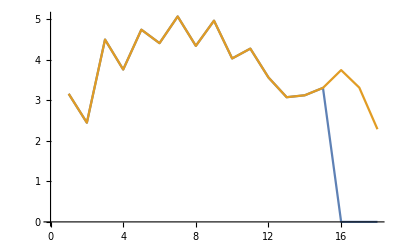

```mathematica
ListLinePlot[{bs2,bs}]
```

```mathematica
bs
```

{2.,2.449489742783178098197284075,3.1622776601683793319988935,4.03319558993444634390547,4.1994014665896887091,4.3642070464842205921,4.79931076189203487,4.708330317759829,4.6820676927078,4.6528555812,4.308479665,4.0026884,3.810389,2.769,3.48,3.,0,Indeterminate,Indeterminate}

```mathematica
as=Append[as,0]
```

{0.,0.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[as]
```

13

```mathematica
Length[bs]
```

14

```mathematica
Im[RetAmpsL4[[4]]]/.t->0
```

0

```mathematica
PTabFrac=AmplitudeCoefficient[as,bs,RetAmpsL4[[2]],tVals,Prec];
```

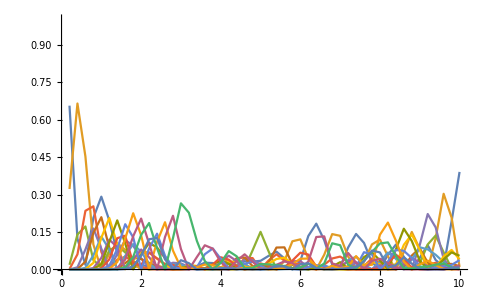

```mathematica
pPlot=Table[Table[{tVals[[j]], Abs[PTabFrac[[n, j]]^2 ] }, {j, 1, Length[tVals]}],{n,1,Length[PTabFrac]}];
ListLinePlot[pPlot, PlotRange->{0,1}]
```

{{0.2,0``-5.572735538297049},{0.4,0``-7.1479380198218845},{0.6,0``-6.204584205516287},{0.8,0``-6.7753052090200425},{1.,0``-6.053338354926288},{1.2,0``-6.249778968947656},{1.4,0``-5.589005198309493},{1.6,0``-5.508819633384135},{1.8,0``-4.969474757359674},{2.,0``-4.390995055594871},{2.2,0``-4.271270509750521},{2.4,0``-4.672954950771112},{2.6,0``-3.9128652636370362},{2.8,0``-4.861101077728688},{3.,0``-5.149648681499195},{3.2,0``-4.984722376717442},{3.4,0``-5.884021389102675},{3.6,0``-5.293449243427836},{3.8,0``-6.402469235610406},{4.,0``-5.7175546451905435},{4.2,0``-6.787622858456277},{4.4,0``-5.746184170671123},{4.6,0``-7.04722572339798},{4.8,0``-5.082230220864},{5.,0``-7.127816329253747},{5.2,0``-4.988434047918696},{5.4,0``-7.014735609728196},{5.6,0``-5.6772428505490415},{5.8,0``-6.731128081354046},{6.,0``-5.570268933319608},{6.2,0``-6.377396279259508},{6.4,0``-5.699609130210782},{6.6,0``-5.98483313008043},{6.8,0``-5.239112686656218},{7.,0``-5.388015921372972},{7.2,0``-5.595417179186559},{7.4,0``-4.760968093182903},{7.6,0``-5.983701862298774},{7.8,0``-5.294551927479345},{8.,0``-6.2820685424039855},{8.2,0``-5.716043926693404},{8.4,0``-6.436227438835138},{8.6,0``-5.79935733259469},{8.8,0``-6.4823705361671955},{9.,0``-5.148972223453705},{9.2,0``-6.639357327853369},{9.4,0``-5.243240980107389},{9.6,0``-6.837002245440405},{9.8,0``-4.950142067924333},{10.,0``-6.936534659870823}}

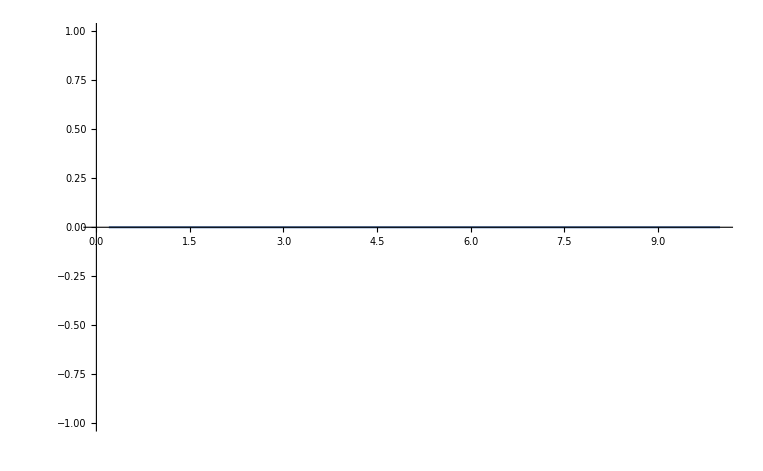

```mathematica
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabFrac[[k, j]]^2 ] , {k, 1, Length[PTabFrac]} ] }, {j, 1, Length[tVals]}]
ListLinePlot[pPlot]
```

### L=5

```mathematica
{as,bs}= LanczosOrthog[TFIMHamiltonian[5,1,1],σx[5],30,30]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0,0,0},{2.5298221281347034655991148355,4.7539457296018851376161486551,3.1129191262745108002428077074,4.4592686596602094546827135628,3.2822564510856624253588947913,4.2181267639972838677645095814,3.2089991151648564951862951774,3.6392997101835390142039402315,0.549993862826667139263217238,4.5921070919991218949761412941,2.2088206026713432109883755026,3.3313383479325367223950988156,2.1530641939979028861609816396,2.5391996217932442347631762295,1.1534353814430325072086805803,2.7950761068691856878446242044,1.2930906220681255226803205444,1.7486786268168991087374010307,0.65939231384579360883260475175,1.5997475746295379863337167004,0,0,0,0,0,0,0,0}}

```mathematica
bs={2.529822128134703465599114835546174826975644111460173461486`30.,4.7539457296018851376161486551455738963055211011349090571969`30.,3.112919126274510800242807707395841216920638916430156277941`30.,4.4592686596602094546827135627908151911388376525144291332339`30.,3.282256451085662425358894791302958855577429224074991955061`30.,4.2181267639972838677645095814436782425291680497188829307647`30.,3.2089991151648564951862951774313279622395485039958609660055`30.,3.639299710183539014203940231458312655694147935605079199201`30.,0.5499938628266671392632172379718385349073568065415263235685`30.,4.5921070919991218949761412941322894283647346902250885699836`30.,2.208820602671343210988375502588810883886854782334405384026`30.,3.3313383479325367223950988156304899134299940979025420327662`30.,2.1530641939979028861609816395943566384573002022578617086644`30.,2.5391996217932442347631762294801648018154668376850896619293`30.,1.1534353814430325072086805803459109864974290688105126227023`30.,2.795076106869185687844624205735967958033895382345775279186`30.,1.2930906220681255226803205114889440604498549684271164836325`30.,1.7486786268168991087373966505229260493164639501676323403658`30.,0.6593923138457936088327192534953922211191660207723069098453`30.,1.5997475746295379863557764056895051976794019237331489240834`30.};
```

```mathematica
as=ConstantArray[0.,Length[bs]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

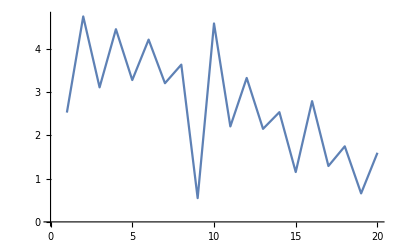

```mathematica
ListLinePlot[bs]
```

```mathematica
PTabFrac=AmplitudeCoefficient[as,bs,RetAmpChopL5[[1]],tVals,Prec];
```

{{0.2,1.},{0.4,1.},{0.6,1.},{0.8,1.},{1.,1.},{1.2,1.},{1.4,1.},{1.6,1.},{1.8,1.},{2.,1.},{2.2,1.},{2.4,1.},{2.6,1.},{2.8,1.},{3.,1.},{3.2,1.},{3.4,1.},{3.6,1.},{3.8,1.},{4.,1.},{4.2,1.},{4.4,1.},{4.6,1.},{4.8,1.},{5.,1.},{5.2,1.},{5.4,1.},{5.6,1.},{5.8,1.},{6.,1.},{6.2,1.},{6.4,1.},{6.6,1.},{6.8,1.},{7.,1.},{7.2,1.},{7.4,1.},{7.6,1.},{7.8,1.},{8.,1.},{8.2,1.},{8.4,1.},{8.6,1.},{8.8,1.},{9.,1.},{9.2,1.},{9.4,1.},{9.6,1.},{9.8,1.},{10.,1.}}

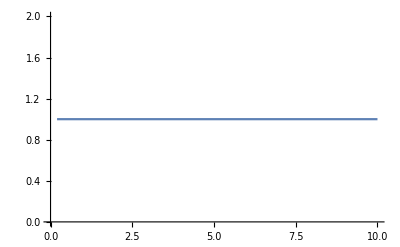

```mathematica
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabFrac[[k, j]]^2 ] , {k, 1, Length[PTabFrac]} ] }, {j, 1, Length[tVals]}]
ListLinePlot[pPlot]
```

### L=6

```mathematica
{as,bs}=LanczosOrthog[HIsing,σz,21,40]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0},{2.,2.58198889747161125678617693318826640722,3.30655913803659851211346970353875061174,4.04366411960676105203625014791365936392,4.29309236599725113137079373286703524584,4.66113230266598488629175417093853861292,5.14207317460845124097613469501838437347,5.35689516139224900334790122238390572923,5.81276118206826082433016799068654188957,6.14816432594982301212878560604146849281,6.34215798579131655357257245826365594921,6.66091574741368047210994334229783077283,6.74582176648277264158853977948939133989,0,0,0,0,0,0}}

```mathematica
{as,bs}=LanczosOrthog[TFIMHamiltonian[6,1,1],σz[6],21,100]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0,0,0,0},{2.,2.58198889747161125678617693318826640722194780352772721772504917740898872795798602234619158457244901,3.30655913803659851211346970353875061174049673782888463777141335663759170494068886365065859527429121,4.0436641196067610520362501479136593639201300249096924875028552861352202876634499139248739842638204,4.29309236599725113137079373286703524583869754883882846740418647046772123306426910161600879545981652,4.66113230266598488629175417093853861291978299727066476213823738559847295780375380121688177398705304,5.14207317460845124097613469501838437346819351190522960033437459884349703149041580496737534777300109,5.35689516139224900334790122238390572922679949932241546929262623679606488831014569066107388083251537,5.81276118206826082433016799068654188957242900222416570851847872696928768850776323093442824161735991,6.14816432594982301212878560604146849280857044414036125664516057841936436096699093610864007204165373,6.34215798579131655357257245826365594920955528171687085698923453690376921903093026415185899684223849,6.6609157474136804721099433422978307728343485754684847795373196168868228792399655621585575524234174,6.74582176648277264158853977948939133989254013405835898421803130538984615296484057828780769335005414,0,0,0,0,0,0}}

```mathematica
bs={2.581988897471611256786176933188266407221947803527727217725`30.,4.7888759989514588947629772501899878088600849242581347035184`30.,3.1519650570604732765500131409839160319249266582383127660839`30.,4.5114029667618885504442214117363473215048521798564844561668`30.,3.3508644073135097577974992660365783770542953735242764459771`30.,4.3347329619958131512812694463497962572664064197532703496787`30.,3.4144176500369101175551552723867784111863333666431082195739`30.,4.1442415941561213964853504048152147715803606434966686948013`30.,3.2934367824382268731373924688253997436399097443676213699662`30.,3.5916729441287458648574370994299962281374430336512122475774`30.,0.6640687934041742489251207689588484725903472174527406788538`30.,5.0635753544302886244039634110673532752437988915228736349414`30.,2.3995005150369026249522873514209870000206319506851000902516`30.,3.751895938826205261262366846861937351260565925581352163723`30.,2.6232728628181354455343814951692685977589395502189943161944`30.,3.3056705700056111412448359635247203175842013815405622093368`30.,2.3765270370395207410538620839023706043673140858375843215631`30.,2.592992803392448440576371229445376882509547189182271817134`30.,1.6356592987787692382365638565791367846008381342908020072929`30.,3.4096584245365387085800198911689709185552925503964098342346`30.,1.6813675396389958837202369728250899038328765163087344956801`30.,2.4760244761280443269376943766967449060862776516864551498275`30.,1.8487469367130245026249634447745947386889078622181113506549`30.,2.052509308079397822732867271171880741051260194505824081272`30.,1.1211615195591077356756585358426320725767060106071450452106`30.,1.9441061408716995896817014264384726811675197040080180954935`30.,1.0254215431585860863671334239168617115394212461635203215554`30.,1.4052305240344079765365421948730912391599963778132688150084`30.,0.5846631612336159278986752449402378284230350911387205720525`30.,1.4576215802234505815139161533643032348559456714295401732329`30.};
as=ConstantArray[0,Length[bs]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

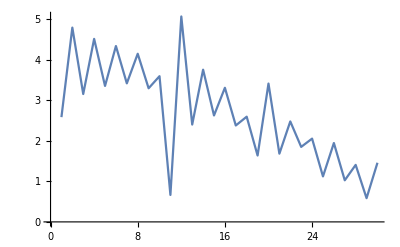

```mathematica
ListLinePlot[bs]
```

```mathematica
PTabFrac=AmplitudeCoefficient[as,bs,RetAmpJacoL6sx,tVals,Prec];
```

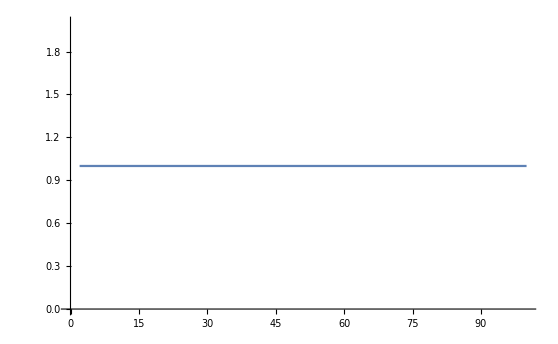

```mathematica
pPlot=Table[{tVals[[j]],Sum[Abs[PTabFrac[[k,j]]^2],{k,1,Length[PTabFrac]}]},{j,1,Length[tVals]}];
ListLinePlot[pPlot]
```

```mathematica
{as,bs}=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Lanczos Coefficients\\bs_Lanczos_HPC_L6_cdMode4.txt","Table", HeaderLines->2];
```

```mathematica
bs=bs[[2;;]];as=as[[2;;]];
```

```mathematica
Length[bs]
Length[as]
```

72

72

```mathematica
rationalizeCoefficients[expr_]:=expr/. {a_?NumericQ x_^b_:>Rationalize[a,0] x^b}
```

```mathematica
RetAmpNew=rationalizeCoefficients[RetAmpJacoL6cd4];
```

```mathematica
PTabFrac=AmplitudeCoefficient[as,bs,RetAmpJacoL6cd4,tVals,100];
```

General::munfl: «1041» (2.66044×10^-308+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (0.+1.88604×10^-308 ⅈ)+4.090410265367019397704972693654710274678834749272781094509586641880851491965147268608757753240079355×10^-312 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.172000955983925586755432277046105667822896298382587128076540169468770106936232616685153244035768919×10^-312-(1.22257×10^-308+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Precision[bs[[71]]]
```

999.964

```mathematica
Precision[as[[1]]]
```

MachinePrecision

```mathematica
as=Table[0,Length[as]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Precision[as[[1]]]
```

∞

```mathematica
Length[PTabFrac]
```

232

```mathematica
bs[[30]]//Precision
```

999.344

```mathematica
Precision[RetAmpJacoL6cd2]
```

34.9185

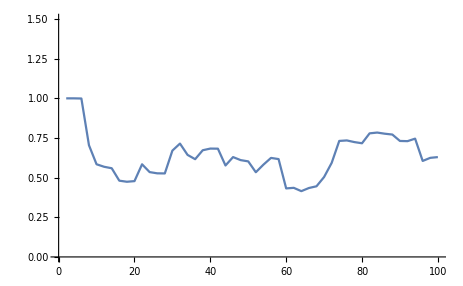

```mathematica
pPlot=Table[{tVals[[j]],Sum[Abs[PTabFrac[[k,j]]^2],{k,1,40}]},{j,1,Length[tVals]}];
ListLinePlot[pPlot,PlotRange->{0,1.5}]
```

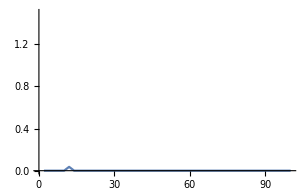

```mathematica
pPlot=Table[{tVals[[j]],Sum[Abs[PTabFrac[[k,j]]^2],{k,90,90}]},{j,1,Length[tVals]}];
ListLinePlot[pPlot,PlotRange->{0,1.5}]
```

```mathematica
Echo[MaxMemoryUsed[], "Memory: "];
```

Memory:   489070536

```mathematica
F[M_]:=Sum[M,{i,1,1000}]
```

```mathematica
Ops={1,2,3,4}
RAs=ParallelMap[F[#]&,Ops]//AbsoluteTiming;
Print[RAs]
```

{1,2,3,4}

{0.0034958,{1000,2000,3000,4000}}

### L=7

```mathematica
bs={2.`30.,2.6457513110645905905016157536392604257102591830824501803684`30.,3.3594217189442420038248561033930760201890229458742181452267`30.,4.036900320208361611653439639413449810236458059899893967247`30.,4.3378272260634483115375937774839035525857162525878668185769`30.,4.7505581300277560885145289600560675864442469747113371952285`30.,5.2069778765123915021254910072993288131762326395928923518628`30.,5.4707788723655920042652513210706789254871991688758696858624`30.,5.9177146257084376556361485588110692279349341932036393828043`30.,6.2268042244842004637116750028895897943581847123444599084832`30.,6.4776196792632994302436125630543339282885405711702835323359`30.,6.8127000338402687811998451749856471315365756541673632236365`30.,6.9929928788372398074765484272423118092117553986575106900388`30.,7.3156834902901750543967218638747550841403342691694109536823`30.,7.5395338790389025630750697638269128150714165884653196343441`30.,7.7715199618895792493613071037006764421069714361898939929703`30.,8.0518898134509999631554102851496170790000054429087124825606`30.,8.2232980197690849715078825061189854839032714182085049380785`30.,8.4972356060198791615948336784450235738802269576313008635077`30.,8.6395320949846014651331673037047546845018583983273398156032`30.,8.8477928844627268671469505518160490595813930109141399508843`30.,9.0039488323300822446823886778991538753293200546566544599598`30.,9.1318428746649945031376374296531688059140620073429956832557`30.,9.3029792282089357894193810265963478234780647071821385375757`30.,9.3744774042147081715523550930515846677649634924742405595393`30.,9.5284265819897721135157185810387480960805122471114563706992`30.,9.5754123380673665383120841727956448331356997919509142817696`30.,9.6801362317893369917219400182208756808012296484826522322972`30.,9.7307214973284614190155891146944365730238110999860706571905`30.,9.7704024880428333858842974593020653924106628061417595546184`30.,9.8280791086694188483083234086161992419105456211701056774632`30.,9.8112237090991641893885855081781960243784954587852687143188`30.,9.8574396221088345533015040020656769063809469228703479596583`30.,9.8089458103493834446365567760275291812274782285788279860746`30.,9.8187824504124167448814698955061039881530073354518954403393`30.,9.7632930630576771507615463517157789067944484325481682216356`30.,9.7179006155217492556148908768235136268021345660704610219135`30.,9.6659392214568545257017205741585674139520334994759343041731`30.,9.566060648607629058444761509575368529458941088093788078681`30.,9.5080617266917515638776212232159035610094818315507783741638`30.,9.3742021968960427224394560848779592217735457511854022684697`30.,9.2878645835433698409646924620698121320187799030250392322182`30.,9.1448951128014533678867252529864094432636703845401514710825`30.,9.0121832455525305308416622117800814055658893855179020212339`30.,8.8834680947100808599174130027451129056911963843820652849029`30.,8.7015010344737144279000539647842772768296911745964378175578`30.,8.6014371474898681128999736354867777345924217266240235383087`30.,8.4049950213067884917700511225161544344090513902546866664719`30.,8.3676491899454608853018834561726081064562457302328039400359`30.,8.2959374066026400122757106387624662154369087400102540365431`30.,8.5446968123779762681559733351927830597017479669848541801324`30.,8.8836175304924636205679916433447381723704176322788408696013`30.,9.5138696531368817977104913239376905394282763309570322975684`30.,9.5505302504697426860704317575385271069609479339768199303081`30.,9.3040882255215299265360384091667150330174587188060287661672`30.,8.6139631139008771728568044280426321952188427972530841575479`30.,8.6651179704116298844144532028037883590375429547874099820527`30.,8.8826666244280030826529391380176542283422655187712423627357`30.,9.5795177004999322788661915338184353618367529666790527153203`30.,8.9835594290526480683483708816167671136036845648428335600518`30.,8.8502012315235012817331492228221855824642137301538410895577`30.,8.3625132395495008783241624057582177103890752110113325949427`30.,9.2011628758474830894533212477685704771279927964167537783256`30.,8.5574661400848240870555441968006313071807370875756994782642`30.,8.9899961766748030876134509135859655082929894674111362278196`30.,8.5709010960951328741555654767121164292797793525066159944663`30.,8.641583895510816404313461251569871819521973023613011188224`30.,8.5642216204447586575551513516867833142550811270001586918523`30.,8.6930146707522755752401020230713810174008119817064928652578`30.,8.4124866853565015528829958735227149134425586975159262418397`30.,8.5380217666744211613281181064658803439857035215215073845753`30.,8.498784792934658949399248693921176369930159055289028850716`30.,8.2949861801110364496321628445142267472232908076348690653957`30.,8.4784047659332135815868303594397778019267347439746543673646`30.,8.2820568579933566059066126356994521763744115124464953286553`30.,8.5283867230456450204983682165128017713646501832793129614226`30.,8.3206021892294646202918070130436218890413746234196634353864`30.,8.7813424815919229354467689864393983663122281539861429590591`30.,8.5847770998752780500779183756442006762119734359167516191709`30.,8.8785779192136580498597079216300365364058359507249805648746`30.,8.767287560079761731672493148002698272678364351978868012407`30.,8.6721541868312461781458400796919171496888756948820624766583`30.,8.6324043358271416121137738338737239817867169007961522796429`30.,8.4596144042733013863975112150583310932153798959775612241981`30.,8.7483059187592837691840871466555777809630853099399385224077`30.,8.5539344981904539617434640196801514743086329921474248094881`30.,8.902991831637723395667555821420099177854826989611539328038`30.,8.5171053753249947378567495086206381464185660915743104054921`30.,8.5243587070593181390003614216419349754245462980650530360687`30.,8.2243479380591915757302147310981411698086924563583248402873`30.,8.1834890360456611095021585470606746157655593368312847210978`30.,8.2513442754861256548441354691743073907577226356305033693078`30.,8.1224461420713218286938848777330308561985390876145462042317`30.,8.3481503700330525631725088503065426809453274485880635944062`30.,8.039100109110438722217687996376381838145986753713625049994`30.,8.2395433328201418238928872851747347543000364842396122818209`30.,8.0686189774207661866597638806650227893925571290523819999991`30.,8.3408989634337299022276175374036533024416201544393825183258`30.,8.4151966127282099289971795187323064968252043680657514382538`30.,8.3358078019839746582035559152194156161604115881455779445047`30.,8.2985430024925140186034508877745345756164458083538346362403`30.,8.0358900677962997992861393498482424006782477731306024382037`30.,8.3800073089193917225869062652424645310209156495021634537277`30.,8.2972024008832731656585303916283143723438599523970886493266`30.,8.2831261899301183971358813898415389542362975144607876467341`30.,7.7817051317982418234957539462569158433687880473164928350593`30.,7.627298136315229343389932627889266953488144411884249031181`30.,7.8368760118551245818520337628433400078001279597523845617352`30.,7.9828886673411275248406005568607304110101464540833006893998`30.,8.15824199265083920703320871104756854581891549586183361445`30.,7.7651994174558109057145425527323047736924218002710651054936`30.,7.9626051028038956583131260226885519937261525104774444122625`30.,8.0443316976482018627692312626213421678355255602319470647433`30.,8.2530692487453475914381704851753884567254931186488963587088`30.,8.0934262352779213588582441930639428367424406745546457870681`30.,7.7927890682791048538192770443385523712452020248920452538844`30.,7.7363029495246332685514229389939457379848222735878387677313`30.,7.5918114557942555634116475724816414288484899861517650945895`30.,7.6585807400691472272319658502629413446773893865938110199186`30.,7.5273323463460265730478268032316275600769276921945041846702`30.,7.5462840261379391198050859144522584867677625936435906185251`30.,7.9787974326150569180381728554027060666935725395457004359767`30.,8.2500561724646418414386048215254471460987459331895597521613`30.,8.4498285124549658682272310201337000333428859146764569402412`30.,8.0843932440273371775939941096536705060376890268546373195088`30.,8.4367214749481920249121083908674383424099580457259151344113`30.,7.6585726821182225482833385497302909850330007161615752604311`30.,7.9879285834154326967218736241500925545963442134012968530967`30.,7.99116025446622311004858712778752474357692728427747350666`30.};
as=ConstantArray[0.,Length[bs]];
```

```mathematica
PTabFrac=AmplitudeCoefficient[as,bs,RetAmpChopL7sz,tVals,Prec];
```

```mathematica
Length[PTabFrac]
```

130

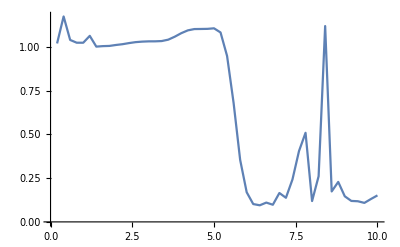

```mathematica
pPlot=Table[{tVals[[j]],Sum[Abs[PTabFrac[[k,j]]^2],{k,1,Length[PTabFrac]-50}]},{j,1,Length[tVals]}];
ListLinePlot[pPlot]
```

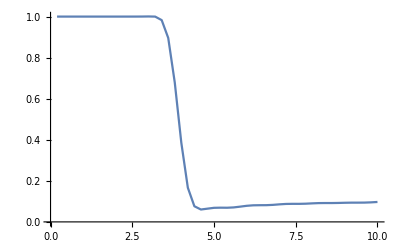

```mathematica
pPlot=Table[{tVals[[j]],Sum[Abs[PTabFrac[[k,j]]^2],{k,1,50}]},{j,1,Length[tVals]}];
ListLinePlot[pPlot]
```

```mathematica
bsL7sp1=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Lanczos Coefficients\\bs_Lanczos_HPC_L7_spMode3.txt","Table", HeaderLines->2][[2]][[2;;]];
as=Table[0,Length[bsL7sp1]];
```

```mathematica
{as,bs}=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Lanczos Coefficients\\bs_Lanczos_HPC_L7_cdMode1.txt","Table", HeaderLines->2];
as=Table[0,Length[as]];bs=bs[[2;;]];
```

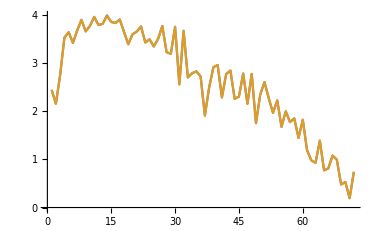

```mathematica
ListLinePlot[{bsL7sp1,bs}]
```

```mathematica
as//Precision
```

∞

```mathematica
Length[as]
```

498

```mathematica
PTabFrac=AmplitudeCoefficient[as,bsL7sp1,RetAmpJacoL7sp3,tVals,300];
```

```mathematica
Length[PTabFrac]
```

73

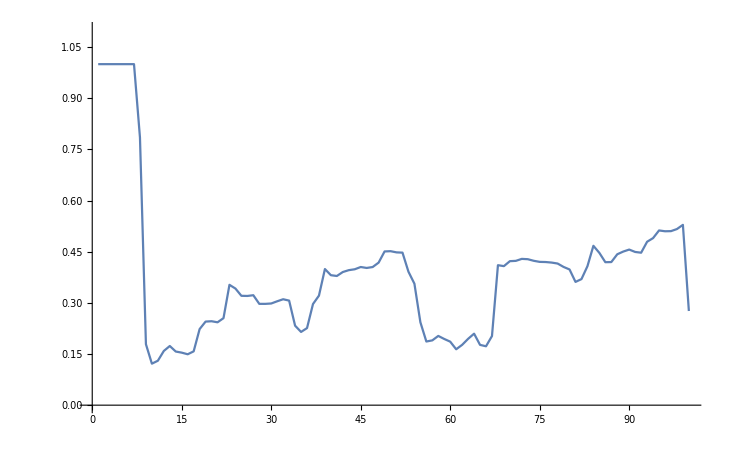

```mathematica
pPlot=Table[{tVals[[j]],Sum[Abs[PTabFrac[[k,j]]^2],{k,1,100}]},{j,1,Length[tVals]}];
ListLinePlot[pPlot, PlotRange->{0,1.1}]
```

### L=8

```mathematica
{as,bs}=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Lanczos Coefficients\\bs_Lanczos_HPC_L8_cdMode4.txt","Table", HeaderLines->2];
```

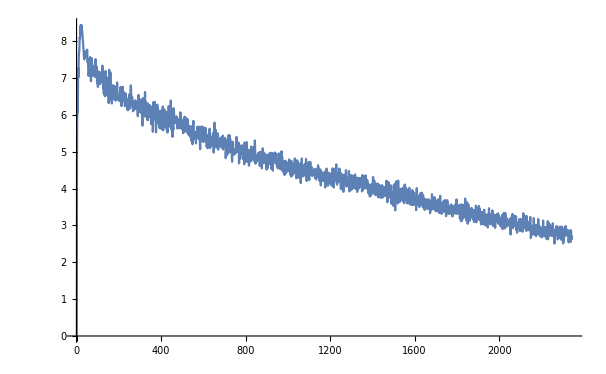

```mathematica
ListLinePlot[bs]
```

```mathematica
bscdMode81//Head
```

String

```mathematica
bscdMode81[[2]]//Head
```

String

```mathematica
Table[]
```

```mathematica
Length[bscdMode81]
```

215

```mathematica
as=ConstantArray[N[0,60],Length[bscdMode81]];
```

```mathematica
PTabFrac=AmplitudeCoefficient[as,bscdMode81,RetAmpJacoL8cd3,tVals,Prec];
```

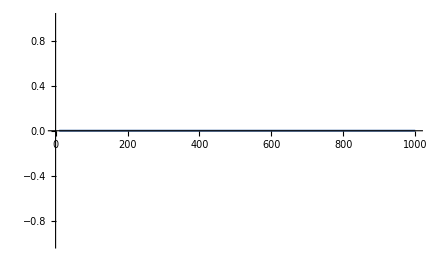

```mathematica
pPlot=Table[{tVals[[j]],Sum[Abs[PTabFrac[[k,j]]^2],{k,1,Length[PTabFrac]}]},{j,1,Length[tVals]}];
ListLinePlot[pPlot]
```

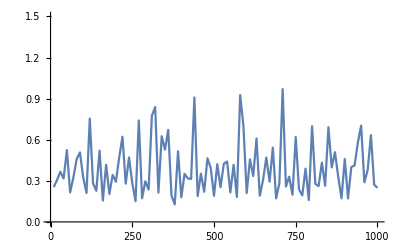

```mathematica
pPlot=Table[{tVals[[j]],Sum[Abs[PTabFrac[[k,j]]^2],{k,1,69}]},{j,1,Length[tVals]}];
ListLinePlot[pPlot, PlotRange->{0,1.5}]
```

## Simplification trickery

```mathematica
RetAmpsL4[[1]]//ByteCount
```

48720

```mathematica
ExpandedRetAmp=Expand[RetAmpsL4[[1]]];
```

```mathematica
Chop[Expand[RetAmpsL4[[1]]],10^(-10)]//ByteCount
```

13272

```mathematica
RetAmpsL5[[1]]//ByteCount
```

219248

```mathematica
Expand[RetAmpsL5[[1]]]//ByteCount
```

197272

```mathematica
Chop[RetAmpsL5[[1]],10^(-21)]//ByteCount
```

43392

```mathematica
ExpL6sx=Expand[RetAmpL6sx];
```

```mathematica
RetAmpL6sx//ByteCount
```

1013704

```mathematica
Chop[RetAmpL6sx,10^(-21)]//ByteCount
```

129272

```mathematica
Chop[RetAmpL6sx, 10^(-3)]//ByteCount
```

129272

```mathematica
ExpL6sx//ByteCount
```

835080

```mathematica
Chop[ExpL6sx,10^(-21)]//ByteCount
```

82792

```mathematica
Chop[ExpL6sx,10^(-6)]//ByteCount
```

82792

```mathematica
Chop[ExpL6sx,10^(-21)]
```

0.615384615384615384615384615384615384615+4.20031283764070169255465854411998626104×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736112 ⅈ t)+4.20031283764070169255465854411998626111×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736112 ⅈ t)+4.20031283764070169255465854411998626056×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736119 ⅈ t)+4.20031283764070169255465854411998626092×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736119 ⅈ t)+4.2003128376407016925546585441199862611×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736131 ⅈ t)+4.20031283764070169255465854411998626097×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736131 ⅈ t)+4.20031283764070169255465854411998626082×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736134 ⅈ t)+4.20031283764070169255465854411998626085×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736134 ⅈ t)+8.40062567528140338510931708823997252121×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736137 ⅈ t)+8.4006256752814033851093170882399725212×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736137 ⅈ t)+4.20031283764070169255465854411998626064×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736142 ⅈ t)+4.20031283764070169255465854411998626064×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736142 ⅈ t)+4.20031283764070169255465854411998626086×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736146 ⅈ t)+4.20031283764070169255465854411998626086×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736146 ⅈ t)+0.0000341397913107697541837501898452045364561 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016286 ⅈ t)+0.0000341397913107697541837501898452045364561 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016286 ⅈ t)+0.0000341397913107697541837501898452045364555 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016288 ⅈ t)+0.0000341397913107697541837501898452045364555 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016288 ⅈ t)+0.0000341397913107697541837501898452045364552 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016288 ⅈ t)+0.0000341397913107697541837501898452045364551 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016288 ⅈ t)+0.0000682795826215395083675003796904090729117 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016288 ⅈ t)+0.0000682795826215395083675003796904090729117 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016288 ⅈ t)+0.0000682795826215395083675003796904090729106 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016289 ⅈ t)+0.0000682795826215395083675003796904090729106 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016289 ⅈ t)+0.0000341397913107697541837501898452045364553 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016292 ⅈ t)+0.0000341397913107697541837501898452045364551 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016292 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638118 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638118 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638119 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638119 ⅈ t)+0.000311563095734229005171897366057900378077 2.718281828459045235360287471352662497757^(-1.57562344451426189065997082840533163812 ⅈ t)+0.000311563095734229005171897366057900378077 2.718281828459045235360287471352662497757^(1.57562344451426189065997082840533163812 ⅈ t)+0.000311563095734229005171897366057900378078 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638121 ⅈ t)+0.000311563095734229005171897366057900378078 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638121 ⅈ t)+0.000155781547867114502585948683028950189038 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638123 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638123 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638123 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638123 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169037 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169037 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169037 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169037 ⅈ t)+0.000694100989297203159189170460658595297389 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169038 ⅈ t)+0.000694100989297203159189170460658595297389 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169038 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169039 ⅈ t)+0.000694100989297203159189170460658595297387 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169039 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169039 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169039 ⅈ t)+0.00138820197859440631837834092131719059478 2.718281828459045235360287471352662497757^(-1.79011226590333099665095948669989216904 ⅈ t)+0.00138820197859440631837834092131719059478 2.718281828459045235360287471352662497757^(1.79011226590333099665095948669989216904 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.79011226590333099665095948669989216904 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(1.79011226590333099665095948669989216904 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(-1.900566269191434717274822320210248226358 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(1.900566269191434717274822320210248226358 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(-1.90056626919143471727482232021024822636 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(1.90056626919143471727482232021024822636 ⅈ t)+0.0310162510787767225689314743381845144321 2.718281828459045235360287471352662497757^(-1.90056626919143471727482232021024822636 ⅈ t)+0.0310162510787767225689314743381845144321 2.718281828459045235360287471352662497757^(1.90056626919143471727482232021024822636 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(-1.900566269191434717274822320210248226362 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(1.900566269191434717274822320210248226362 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(-1.900566269191434717274822320210248226363 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(1.900566269191434717274822320210248226363 ⅈ t)+0.0000140514953322499311379743015531802184324 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011731 ⅈ t)+0.0000140514953322499311379743015531802184329 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011731 ⅈ t)+0.0000281029906644998622759486031063604368664 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011733 ⅈ t)+0.0000281029906644998622759486031063604368664 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011733 ⅈ t)+0.0000140514953322499311379743015531802184333 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011734 ⅈ t)+0.0000140514953322499311379743015531802184333 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011734 ⅈ t)+0.000028102990664499862275948603106360436866 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011734 ⅈ t)+0.0000281029906644998622759486031063604368657 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011734 ⅈ t)+0.0000140514953322499311379743015531802184326 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011735 ⅈ t)+0.0000140514953322499311379743015531802184326 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011735 ⅈ t)+0.0000140514953322499311379743015531802184327 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011736 ⅈ t)+0.0000140514953322499311379743015531802184327 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011736 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(-3.059677381591547370205231338250221185326 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(3.059677381591547370205231338250221185326 ⅈ t)+0.000207398134347050527539559276941611206714 2.718281828459045235360287471352662497757^(-3.059677381591547370205231338250221185327 ⅈ t)+0.000207398134347050527539559276941611206714 2.718281828459045235360287471352662497757^(3.059677381591547370205231338250221185327 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(-3.059677381591547370205231338250221185328 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(3.059677381591547370205231338250221185328 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(-3.059677381591547370205231338250221185329 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(3.059677381591547370205231338250221185329 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864478 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864478 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(-3.47618971370569660793479314861557986448 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(3.47618971370569660793479314861557986448 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864481 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864481 ⅈ t)+0.00162555409914095921180348837614528891238 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864481 ⅈ t)+0.00162555409914095921180348837614528891238 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864481 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864483 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864483 ⅈ t)+0.000541851366380319737267829458715096304127 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864485 ⅈ t)+0.000541851366380319737267829458715096304128 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864485 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(-3.690678535094765713925781806910140395397 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(3.690678535094765713925781806910140395397 ⅈ t)+0.0192239141290986344624186661336532874821 2.718281828459045235360287471352662497757^(-3.690678535094765713925781806910140395399 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(3.690678535094765713925781806910140395399 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(3.6906785350947657139257818069101403954 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(-3.6906785350947657139257818069101403954 ⅈ t)+0.00640797137636621148747288871121776249404 2.718281828459045235360287471352662497757^(3.6906785350947657139257818069101403954 ⅈ t)+0.00640797137636621148747288871121776249404 2.718281828459045235360287471352662497757^(-3.690678535094765713925781806910140395401 ⅈ t)+0.00640797137636621148747288871121776249404 2.718281828459045235360287471352662497757^(3.690678535094765713925781806910140395401 ⅈ t)+0.0000769655461403091512748574876098721212183 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238092 ⅈ t)+0.000115448319210463726912286231414808181826 2.718281828459045235360287471352662497757^(4.365913990725500322024199854985331238092 ⅈ t)+0.000038482773070154575637428743804936060608 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238093 ⅈ t)+0.0000769655461403091512748574876098721212159 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238094 ⅈ t)+0.0000769655461403091512748574876098721212159 2.718281828459045235360287471352662497757^(4.365913990725500322024199854985331238094 ⅈ t)+0.0000384827730701545756374287438049360606095 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238096 ⅈ t)+0.0000384827730701545756374287438049360606095 2.718281828459045235360287471352662497757^(4.365913990725500322024199854985331238096 ⅈ t)+0.0000769655461403091512748574876098721212156 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238097 ⅈ t)+0.0000769655461403091512748574876098721212158 2.718281828459045235360287471352662497757^(4.365913990725500322024199854985331238097 ⅈ t)+0.000660759635400672303496894153049460912767 2.718281828459045235360287471352662497757^(-4.960243650782982087480053658460469411686 ⅈ t)+0.000660759635400672303496894153049460912767 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411686 ⅈ t)+0.000991139453101008455245341229574191369148 2.718281828459045235360287471352662497757^(-4.960243650782982087480053658460469411687 ⅈ t)+0.000660759635400672303496894153049460912765 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411687 ⅈ t)+0.000330379817700336151748447076524730456383 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411688 ⅈ t)+0.000660759635400672303496894153049460912765 2.718281828459045235360287471352662497757^(-4.960243650782982087480053658460469411689 ⅈ t)+0.000660759635400672303496894153049460912765 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411689 ⅈ t)+0.000330379817700336151748447076524730456382 2.718281828459045235360287471352662497757^(-4.960243650782982087480053658460469411691 ⅈ t)+0.000330379817700336151748447076524730456382 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411691 ⅈ t)+0.00902065133621901347486283631001033002181 2.718281828459045235360287471352662497757^(-5.266301979609027604585752635315472033518 ⅈ t)+0.00902065133621901347486283631001033002181 2.718281828459045235360287471352662497757^(5.266301979609027604585752635315472033518 ⅈ t)+0.0135309770043285202122942544650154950327 2.718281828459045235360287471352662497757^(-5.266301979609027604585752635315472033519 ⅈ t)+0.00902065133621901347486283631001033002181 2.718281828459045235360287471352662497757^(5.266301979609027604585752635315472033519 ⅈ t)+0.0135309770043285202122942544650154950327 2.718281828459045235360287471352662497757^(5.26630197960902760458575263531547203352 ⅈ t)+0.00902065133621901347486283631001033002181 2.718281828459045235360287471352662497757^(-5.266301979609027604585752635315472033521 ⅈ t)+0.0045103256681095067374314181550051650109 2.718281828459045235360287471352662497757^(-5.266301979609027604585752635315472033523 ⅈ t)+0.0045103256681095067374314181550051650109 2.718281828459045235360287471352662497757^(5.266301979609027604585752635315472033523 ⅈ t)+0.000117845184997631015945444707421870847878 2.718281828459045235360287471352662497757^(-6.15602625662883131867515934168522340713 ⅈ t)+0.000117845184997631015945444707421870847878 2.718281828459045235360287471352662497757^(6.15602625662883131867515934168522340713 ⅈ t)+0.000235690369995262031890889414843741695756 2.718281828459045235360287471352662497757^(-6.156026256628831318675159341685223407132 ⅈ t)+0.000235690369995262031890889414843741695756 2.718281828459045235360287471352662497757^(6.156026256628831318675159341685223407132 ⅈ t)+0.000353535554992893047836334122265612543636 2.718281828459045235360287471352662497757^(-6.156026256628831318675159341685223407133 ⅈ t)+0.000353535554992893047836334122265612543636 2.718281828459045235360287471352662497757^(6.156026256628831318675159341685223407133 ⅈ t)+0.000235690369995262031890889414843741695756 2.718281828459045235360287471352662497757^(-6.156026256628831318675159341685223407135 ⅈ t)+0.000235690369995262031890889414843741695756 2.718281828459045235360287471352662497757^(6.156026256628831318675159341685223407135 ⅈ t)+0.00249697572049875203787798344291642961238 2.718281828459045235360287471352662497757^(-6.535867095297243978140024486865801049806 ⅈ t)+0.00249697572049875203787798344291642961238 2.718281828459045235360287471352662497757^(6.535867095297243978140024486865801049806 ⅈ t)+0.00998790288199500815151193377166571844954 2.718281828459045235360287471352662497757^(-6.535867095297243978140024486865801049807 ⅈ t)+0.00749092716149625611363395032874928883715 2.718281828459045235360287471352662497757^(6.535867095297243978140024486865801049807 ⅈ t)+0.00249697572049875203787798344291642961238 2.718281828459045235360287471352662497757^(6.535867095297243978140024486865801049809 ⅈ t)+0.00749092716149625611363395032874928883715 2.718281828459045235360287471352662497757^(-6.53586709529724397814002448686580104981 ⅈ t)+0.00749092716149625611363395032874928883715 2.718281828459045235360287471352662497757^(6.53586709529724397814002448686580104981 ⅈ t)+0.000834593657825942763364974726208563236245 2.718281828459045235360287471352662497757^(-7.425591372317047692229431193235552423418 ⅈ t)+0.000834593657825942763364974726208563236245 2.718281828459045235360287471352662497757^(7.425591372317047692229431193235552423418 ⅈ t)+0.000834593657825942763364974726208563236245 2.718281828459045235360287471352662497757^(-7.425591372317047692229431193235552423421 ⅈ t)+0.000834593657825942763364974726208563236245 2.718281828459045235360287471352662497757^(7.425591372317047692229431193235552423421 ⅈ t)+0.00333837463130377105345989890483425294498 2.718281828459045235360287471352662497757^(-7.425591372317047692229431193235552423422 ⅈ t)+0.00333837463130377105345989890483425294498 2.718281828459045235360287471352662497757^(7.425591372317047692229431193235552423422 ⅈ t)+0.00166918731565188552672994945241712647249 2.718281828459045235360287471352662497757^(-7.425591372317047692229431193235552423424 ⅈ t)+0.00166918731565188552672994945241712647249 2.718281828459045235360287471352662497757^(7.425591372317047692229431193235552423424 ⅈ t)

```mathematica
someplot=Simplify[Chop[ExpL6sx,10^(-10)]]
```

0.6154+0.0000336 ⅇ^(-0.88972427701980371408940670636975137 ⅈ t)+0.0000336 ⅇ^(0.88972427701980371408940670636975137 ⅈ t)+0.0002731 ⅇ^(-1.26956511568821637355427185155032902 ⅈ t)+0.0002731 ⅇ^(1.26956511568821637355427185155032902 ⅈ t)+0.001246 ⅇ^(-1.57562344451426189065997082840533164 ⅈ t)+0.001246 ⅇ^(1.57562344451426189065997082840533164 ⅈ t)+0.005553 ⅇ^(-1.79011226590333099665095948669989217 ⅈ t)+0.005553 ⅇ^(1.79011226590333099665095948669989217 ⅈ t)+0.06203 ⅇ^(-1.90056626919143471727482232021024823 ⅈ t)+0.06203 ⅇ^(1.90056626919143471727482232021024823 ⅈ t)+0.0001124 ⅇ^(-2.46534772153406560474937753477508301 ⅈ t)+0.0001124 ⅇ^(2.46534772153406560474937753477508301 ⅈ t)+0.0008296 ⅇ^(-3.05967738159154737020523133825022119 ⅈ t)+0.0008296 ⅇ^(3.05967738159154737020523133825022119 ⅈ t)+0.004335 ⅇ^(-3.47618971370569660793479314861557986 ⅈ t)+0.004335 ⅇ^(3.47618971370569660793479314861557986 ⅈ t)+0.05126 ⅇ^(-3.6906785350947657139257818069101404 ⅈ t)+0.05126 ⅇ^(3.6906785350947657139257818069101404 ⅈ t)+0.0003079 ⅇ^(-4.36591399072550032202419985498533124 ⅈ t)+0.0003079 ⅇ^(4.36591399072550032202419985498533124 ⅈ t)+0.002643 ⅇ^(-4.96024365078298208748005365846046941 ⅈ t)+0.002643 ⅇ^(4.96024365078298208748005365846046941 ⅈ t)+0.03608 ⅇ^(-5.26630197960902760458575263531547203 ⅈ t)+0.03608 ⅇ^(5.26630197960902760458575263531547203 ⅈ t)+0.0009428 ⅇ^(-6.15602625662883131867515934168522341 ⅈ t)+0.0009428 ⅇ^(6.15602625662883131867515934168522341 ⅈ t)+0.01998 ⅇ^(-6.53586709529724397814002448686580105 ⅈ t)+0.01998 ⅇ^(6.53586709529724397814002448686580105 ⅈ t)+0.006677 ⅇ^(-7.42559137231704769222943119323555242 ⅈ t)+0.006677 ⅇ^(7.42559137231704769222943119323555242 ⅈ t)

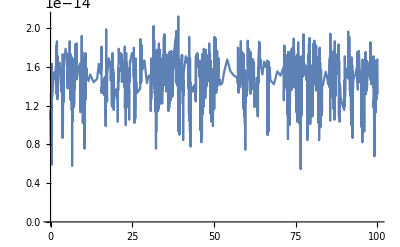

```mathematica
Plot[Re[someplot]-RetAmpL6sx,{t,0,100},PlotRange->{0,Automatic}]
```

```mathematica
Collect[Chop[ExpL6sx,10^-10],Exp[_]]
```

0.615384615384615384615384615384615384615+4.20031283764070169255465854411998626104×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736112 ⅈ t)+4.20031283764070169255465854411998626111×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736112 ⅈ t)+4.20031283764070169255465854411998626056×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736119 ⅈ t)+4.20031283764070169255465854411998626092×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736119 ⅈ t)+4.2003128376407016925546585441199862611×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736131 ⅈ t)+4.20031283764070169255465854411998626097×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736131 ⅈ t)+4.20031283764070169255465854411998626082×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736134 ⅈ t)+4.20031283764070169255465854411998626085×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736134 ⅈ t)+8.40062567528140338510931708823997252121×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736137 ⅈ t)+8.4006256752814033851093170882399725212×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736137 ⅈ t)+4.20031283764070169255465854411998626064×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736142 ⅈ t)+4.20031283764070169255465854411998626064×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736142 ⅈ t)+4.20031283764070169255465854411998626086×10^-6 2.718281828459045235360287471352662497757^(-0.8897242770198037140894067063697513736146 ⅈ t)+4.20031283764070169255465854411998626086×10^-6 2.718281828459045235360287471352662497757^(0.8897242770198037140894067063697513736146 ⅈ t)+0.0000341397913107697541837501898452045364561 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016286 ⅈ t)+0.0000341397913107697541837501898452045364561 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016286 ⅈ t)+0.0000341397913107697541837501898452045364555 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016288 ⅈ t)+0.0000341397913107697541837501898452045364555 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016288 ⅈ t)+0.0000341397913107697541837501898452045364552 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016288 ⅈ t)+0.0000341397913107697541837501898452045364551 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016288 ⅈ t)+0.0000682795826215395083675003796904090729117 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016288 ⅈ t)+0.0000682795826215395083675003796904090729117 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016288 ⅈ t)+0.0000682795826215395083675003796904090729106 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016289 ⅈ t)+0.0000682795826215395083675003796904090729106 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016289 ⅈ t)+0.0000341397913107697541837501898452045364553 2.718281828459045235360287471352662497757^(-1.269565115688216373554271851550329016292 ⅈ t)+0.0000341397913107697541837501898452045364551 2.718281828459045235360287471352662497757^(1.269565115688216373554271851550329016292 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638118 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638118 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638119 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638119 ⅈ t)+0.000311563095734229005171897366057900378077 2.718281828459045235360287471352662497757^(-1.57562344451426189065997082840533163812 ⅈ t)+0.000311563095734229005171897366057900378077 2.718281828459045235360287471352662497757^(1.57562344451426189065997082840533163812 ⅈ t)+0.000311563095734229005171897366057900378078 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638121 ⅈ t)+0.000311563095734229005171897366057900378078 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638121 ⅈ t)+0.000155781547867114502585948683028950189038 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638123 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638123 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(-1.575623444514261890659970828405331638123 ⅈ t)+0.000155781547867114502585948683028950189039 2.718281828459045235360287471352662497757^(1.575623444514261890659970828405331638123 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169037 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169037 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169037 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169037 ⅈ t)+0.000694100989297203159189170460658595297389 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169038 ⅈ t)+0.000694100989297203159189170460658595297389 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169038 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169039 ⅈ t)+0.000694100989297203159189170460658595297387 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169039 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.790112265903330996650959486699892169039 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(1.790112265903330996650959486699892169039 ⅈ t)+0.00138820197859440631837834092131719059478 2.718281828459045235360287471352662497757^(-1.79011226590333099665095948669989216904 ⅈ t)+0.00138820197859440631837834092131719059478 2.718281828459045235360287471352662497757^(1.79011226590333099665095948669989216904 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(-1.79011226590333099665095948669989216904 ⅈ t)+0.000694100989297203159189170460658595297388 2.718281828459045235360287471352662497757^(1.79011226590333099665095948669989216904 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(-1.900566269191434717274822320210248226358 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(1.900566269191434717274822320210248226358 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(-1.90056626919143471727482232021024822636 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(1.90056626919143471727482232021024822636 ⅈ t)+0.0310162510787767225689314743381845144321 2.718281828459045235360287471352662497757^(-1.90056626919143471727482232021024822636 ⅈ t)+0.0310162510787767225689314743381845144321 2.718281828459045235360287471352662497757^(1.90056626919143471727482232021024822636 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(-1.900566269191434717274822320210248226362 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(1.900566269191434717274822320210248226362 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(-1.900566269191434717274822320210248226363 ⅈ t)+0.00775406276969418064223286858454612860804 2.718281828459045235360287471352662497757^(1.900566269191434717274822320210248226363 ⅈ t)+0.0000140514953322499311379743015531802184324 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011731 ⅈ t)+0.0000140514953322499311379743015531802184329 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011731 ⅈ t)+0.0000281029906644998622759486031063604368664 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011733 ⅈ t)+0.0000281029906644998622759486031063604368664 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011733 ⅈ t)+0.0000140514953322499311379743015531802184333 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011734 ⅈ t)+0.0000140514953322499311379743015531802184333 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011734 ⅈ t)+0.000028102990664499862275948603106360436866 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011734 ⅈ t)+0.0000281029906644998622759486031063604368657 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011734 ⅈ t)+0.0000140514953322499311379743015531802184326 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011735 ⅈ t)+0.0000140514953322499311379743015531802184326 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011735 ⅈ t)+0.0000140514953322499311379743015531802184327 2.718281828459045235360287471352662497757^(-2.465347721534065604749377534775083011736 ⅈ t)+0.0000140514953322499311379743015531802184327 2.718281828459045235360287471352662497757^(2.465347721534065604749377534775083011736 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(-3.059677381591547370205231338250221185326 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(3.059677381591547370205231338250221185326 ⅈ t)+0.000207398134347050527539559276941611206714 2.718281828459045235360287471352662497757^(-3.059677381591547370205231338250221185327 ⅈ t)+0.000207398134347050527539559276941611206714 2.718281828459045235360287471352662497757^(3.059677381591547370205231338250221185327 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(-3.059677381591547370205231338250221185328 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(3.059677381591547370205231338250221185328 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(-3.059677381591547370205231338250221185329 ⅈ t)+0.000207398134347050527539559276941611206715 2.718281828459045235360287471352662497757^(3.059677381591547370205231338250221185329 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864478 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864478 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(-3.47618971370569660793479314861557986448 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(3.47618971370569660793479314861557986448 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864481 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864481 ⅈ t)+0.00162555409914095921180348837614528891238 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864481 ⅈ t)+0.00162555409914095921180348837614528891238 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864481 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864483 ⅈ t)+0.000541851366380319737267829458715096304126 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864483 ⅈ t)+0.000541851366380319737267829458715096304127 2.718281828459045235360287471352662497757^(-3.476189713705696607934793148615579864485 ⅈ t)+0.000541851366380319737267829458715096304128 2.718281828459045235360287471352662497757^(3.476189713705696607934793148615579864485 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(-3.690678535094765713925781806910140395397 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(3.690678535094765713925781806910140395397 ⅈ t)+0.0192239141290986344624186661336532874821 2.718281828459045235360287471352662497757^(-3.690678535094765713925781806910140395399 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(3.690678535094765713925781806910140395399 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(3.6906785350947657139257818069101403954 ⅈ t)+0.0128159427527324229749457774224355249881 2.718281828459045235360287471352662497757^(-3.6906785350947657139257818069101403954 ⅈ t)+0.00640797137636621148747288871121776249404 2.718281828459045235360287471352662497757^(3.6906785350947657139257818069101403954 ⅈ t)+0.00640797137636621148747288871121776249404 2.718281828459045235360287471352662497757^(-3.690678535094765713925781806910140395401 ⅈ t)+0.00640797137636621148747288871121776249404 2.718281828459045235360287471352662497757^(3.690678535094765713925781806910140395401 ⅈ t)+0.0000769655461403091512748574876098721212183 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238092 ⅈ t)+0.000115448319210463726912286231414808181826 2.718281828459045235360287471352662497757^(4.365913990725500322024199854985331238092 ⅈ t)+0.000038482773070154575637428743804936060608 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238093 ⅈ t)+0.0000769655461403091512748574876098721212159 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238094 ⅈ t)+0.0000769655461403091512748574876098721212159 2.718281828459045235360287471352662497757^(4.365913990725500322024199854985331238094 ⅈ t)+0.0000384827730701545756374287438049360606095 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238096 ⅈ t)+0.0000384827730701545756374287438049360606095 2.718281828459045235360287471352662497757^(4.365913990725500322024199854985331238096 ⅈ t)+0.0000769655461403091512748574876098721212156 2.718281828459045235360287471352662497757^(-4.365913990725500322024199854985331238097 ⅈ t)+0.0000769655461403091512748574876098721212158 2.718281828459045235360287471352662497757^(4.365913990725500322024199854985331238097 ⅈ t)+0.000660759635400672303496894153049460912767 2.718281828459045235360287471352662497757^(-4.960243650782982087480053658460469411686 ⅈ t)+0.000660759635400672303496894153049460912767 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411686 ⅈ t)+0.000991139453101008455245341229574191369148 2.718281828459045235360287471352662497757^(-4.960243650782982087480053658460469411687 ⅈ t)+0.000660759635400672303496894153049460912765 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411687 ⅈ t)+0.000330379817700336151748447076524730456383 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411688 ⅈ t)+0.000660759635400672303496894153049460912765 2.718281828459045235360287471352662497757^(-4.960243650782982087480053658460469411689 ⅈ t)+0.000660759635400672303496894153049460912765 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411689 ⅈ t)+0.000330379817700336151748447076524730456382 2.718281828459045235360287471352662497757^(-4.960243650782982087480053658460469411691 ⅈ t)+0.000330379817700336151748447076524730456382 2.718281828459045235360287471352662497757^(4.960243650782982087480053658460469411691 ⅈ t)+0.00902065133621901347486283631001033002181 2.718281828459045235360287471352662497757^(-5.266301979609027604585752635315472033518 ⅈ t)+0.00902065133621901347486283631001033002181 2.718281828459045235360287471352662497757^(5.266301979609027604585752635315472033518 ⅈ t)+0.0135309770043285202122942544650154950327 2.718281828459045235360287471352662497757^(-5.266301979609027604585752635315472033519 ⅈ t)+0.00902065133621901347486283631001033002181 2.718281828459045235360287471352662497757^(5.266301979609027604585752635315472033519 ⅈ t)+0.0135309770043285202122942544650154950327 2.718281828459045235360287471352662497757^(5.26630197960902760458575263531547203352 ⅈ t)+0.00902065133621901347486283631001033002181 2.718281828459045235360287471352662497757^(-5.266301979609027604585752635315472033521 ⅈ t)+0.0045103256681095067374314181550051650109 2.718281828459045235360287471352662497757^(-5.266301979609027604585752635315472033523 ⅈ t)+0.0045103256681095067374314181550051650109 2.718281828459045235360287471352662497757^(5.266301979609027604585752635315472033523 ⅈ t)+0.000117845184997631015945444707421870847878 2.718281828459045235360287471352662497757^(-6.15602625662883131867515934168522340713 ⅈ t)+0.000117845184997631015945444707421870847878 2.718281828459045235360287471352662497757^(6.15602625662883131867515934168522340713 ⅈ t)+0.000235690369995262031890889414843741695756 2.718281828459045235360287471352662497757^(-6.156026256628831318675159341685223407132 ⅈ t)+0.000235690369995262031890889414843741695756 2.718281828459045235360287471352662497757^(6.156026256628831318675159341685223407132 ⅈ t)+0.000353535554992893047836334122265612543636 2.718281828459045235360287471352662497757^(-6.156026256628831318675159341685223407133 ⅈ t)+0.000353535554992893047836334122265612543636 2.718281828459045235360287471352662497757^(6.156026256628831318675159341685223407133 ⅈ t)+0.000235690369995262031890889414843741695756 2.718281828459045235360287471352662497757^(-6.156026256628831318675159341685223407135 ⅈ t)+0.000235690369995262031890889414843741695756 2.718281828459045235360287471352662497757^(6.156026256628831318675159341685223407135 ⅈ t)+0.00249697572049875203787798344291642961238 2.718281828459045235360287471352662497757^(-6.535867095297243978140024486865801049806 ⅈ t)+0.00249697572049875203787798344291642961238 2.718281828459045235360287471352662497757^(6.535867095297243978140024486865801049806 ⅈ t)+0.00998790288199500815151193377166571844954 2.718281828459045235360287471352662497757^(-6.535867095297243978140024486865801049807 ⅈ t)+0.00749092716149625611363395032874928883715 2.718281828459045235360287471352662497757^(6.535867095297243978140024486865801049807 ⅈ t)+0.00249697572049875203787798344291642961238 2.718281828459045235360287471352662497757^(6.535867095297243978140024486865801049809 ⅈ t)+0.00749092716149625611363395032874928883715 2.718281828459045235360287471352662497757^(-6.53586709529724397814002448686580104981 ⅈ t)+0.00749092716149625611363395032874928883715 2.718281828459045235360287471352662497757^(6.53586709529724397814002448686580104981 ⅈ t)+0.000834593657825942763364974726208563236245 2.718281828459045235360287471352662497757^(-7.425591372317047692229431193235552423418 ⅈ t)+0.000834593657825942763364974726208563236245 2.718281828459045235360287471352662497757^(7.425591372317047692229431193235552423418 ⅈ t)+0.000834593657825942763364974726208563236245 2.718281828459045235360287471352662497757^(-7.425591372317047692229431193235552423421 ⅈ t)+0.000834593657825942763364974726208563236245 2.718281828459045235360287471352662497757^(7.425591372317047692229431193235552423421 ⅈ t)+0.00333837463130377105345989890483425294498 2.718281828459045235360287471352662497757^(-7.425591372317047692229431193235552423422 ⅈ t)+0.00333837463130377105345989890483425294498 2.718281828459045235360287471352662497757^(7.425591372317047692229431193235552423422 ⅈ t)+0.00166918731565188552672994945241712647249 2.718281828459045235360287471352662497757^(-7.425591372317047692229431193235552423424 ⅈ t)+0.00166918731565188552672994945241712647249 2.718281828459045235360287471352662497757^(7.425591372317047692229431193235552423424 ⅈ t)

### random expr

```mathematica
expr=0.8367082Exp[0.08038I*t] +0.00973972Exp[0.67392*I*t] +Exp[0.8320*I*t] +0.003Exp[0.8320*I*t]
```

0.836708 ⅇ^((0.+0.08038 ⅈ) t)+0.00973972 ⅇ^((0.+0.67392 ⅈ) t)+1.003 ⅇ^((0.+0.832 ⅈ) t)

```mathematica
Rationalize[expr,0]
```

(4183541 ⅇ^((4019 ⅈ t)/50000))/5000000+(243493 ⅇ^((2106 ⅈ t)/3125))/25000000+(1003 ⅇ^((104 ⅈ t)/125))/1000

```mathematica
Rationalize[expr,0]//N
```

0.836708 2.71828^((0.+0.08038 ⅈ) t)+0.00973972 2.71828^((0.+0.67392 ⅈ) t)+1.003 2.71828^((0.+0.832 ⅈ) t)

```mathematica
Collect[expr,Exp[_]]
```

0.836708 ⅇ^((0.+0.08038 ⅈ) t)+0.00973972 ⅇ^((0.+0.67392 ⅈ) t)+1.003 ⅇ^((0.+0.832 ⅈ) t)

Expand, Chop, Rationalize coeffs, Simplify, Unrationalize coeffs
Expand, Chop, Group by Exponentials, Parallel simplify

## Testing package

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\daisy\OneDrive - University of Cape Town\0. Masters Project\Return Amplitudes

```mathematica
Get["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Ising_matrices_package.wl"];
```

```mathematica
σx[2]
```

{{0,1,1,0},{1,0,0,1},{1,0,0,1},{0,1,1,0}}

```mathematica
σPlus[2]
```

{{0,1,1,0},{0,0,0,1},{0,0,0,1},{0,0,0,0}}

```mathematica
σxMode[2,1]
```

{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}

```mathematica
σxMode[2,2]
```

{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
σzMode
```